```mathematica
Clear[pm,partialTrace, single, czGate, channel];
pm[i_]:= PauliMatrix[i];

partialTrace[matrix_,lengths_,indicesToKeep_]:=
(*matrix: input state. lengths are the dimensions e.g. 3 qubits {2,2,2,2}. indicesToKeep: qubits to keep.*)
With[{indicesToTrace=Complement[Range@Length@lengths,indicesToKeep]},With[{matrixInTPForm=Transpose[ArrayReshape[matrix,Join[lengths,lengths]],Join@@Transpose@Partition[Range[2 Length@lengths],2]]},Flatten[TensorContract[matrixInTPForm,{2 #-1,2 #}&/@indicesToTrace],Transpose@Partition[Range[2 Length@lengths-2 Length@indicesToTrace],2]]]];

single[n_,switch_,matrix_]:= (*n: number of qubits. switch: qubit to apply matrix to*)KroneckerProduct@@ReplacePart[ConstantArray[IdentityMatrix[2],n],switch->matrix];

cxGate[n_,control_,target_]:=Divide[1,2](IdentityMatrix[2^n]+single[n, control, pm[3]]+single[n,target,pm[1]]-single[n, control, pm[3]].single[n,target,pm[1]]);
czGate[n_,control_,target_]:= Divide[1,2](IdentityMatrix[2^n]+single[n, control, pm[3]]+single[n,target,pm[3]]-single[n, control, pm[3]].single[n,target,pm[3]]);

channel[n_,switch_,p_,state_]:= 
(*Depolarizing channel. n: number of qubits. switch: qubit sent into the channel. p is the probability. state: is the input.*)
(1-Divide[3p,4])state+Divide[p,4]Sum[single[n,switch,PauliMatrix[i]].state.single[n,switch,PauliMatrix[i]],{i,1,3}];

zMeas[0] = {{1,0},{0,0}};
zMeas[1] = {{0,0},{0,1}};
```

```mathematica
partialTrace[UnitVector[2^8,1],{2,2,2,2,2,2,2,2},{8}]
```

{{1,0},{0,0}}

```mathematica
ket0={{1},{0}};
ket1={{0},{1}};
bra0=Transpose[ket0];
bra1=Transpose[ket1];
ketPlus=1/Sqrt[2](ket0+ket1);
ketPhiPlus=1/Sqrt[2](KroneckerProduct[ket0,ket0]+KroneckerProduct[ket1, ket1]);
rhoPhiPlus=ketPhiPlus.Transpose[ketPhiPlus];
rhoPlus=ketPlus.Transpose[ketPlus];
```

```mathematica
nqubits=4;
rho0=KroneckerProduct[rhoPlus, rhoPlus, rhoPhiPlus]; (*State before left checks*)
pcsLeftU=cxGate[nqubits,1,3].cxGate[nqubits,2,4]; 
pcsRightU=Transpose[pcsLeftU];
rho1=pcsLeftU.rho0.Transpose[pcsLeftU]; (*left PCS checks*)
rho2=rho1;
rho2=FullSimplify[channel[nqubits,1,p1,  rho2]];
rho2=FullSimplify[channel[nqubits,2,p2,  rho2]];
rho2=FullSimplify[channel[nqubits,3,p1,  rho2]];
rho2=FullSimplify[channel[nqubits,4,p2,  rho2]];(*State after noise*)
rho3=pcsRightU.rho2.Transpose[pcsRightU]; (*right PCS checks.*)
(*Post measurement state unormalized*)
rho4=FullSimplify[single[nqubits, 1, rhoPlus].single[nqubits, 2, rhoPlus].rho3.single[nqubits, 1, rhoPlus].single[nqubits, 2, rhoPlus]];
finalNormalizedSt=FullSimplify[rho4/Tr[rho4]];
noisyBellSt=partialTrace[finalNormalizedSt,{2,2,2,2}, {3,4}](*Final normalized state*)
```

{{(8+6 (-2+p2) p2-2 p1 (6+5 (-2+p2) p2)+p1^2 (6+5 (-2+p2) p2))/(4 (2+(-2+p1) p1) (2+(-2+p2) p2)),0,0,((-1+p1) (2+p1 (-1+p2)-p2) (-1+p2))/((2+(-2+p1) p1) (2+(-2+p2) p2))},{0,(-2 (-2+p1) p1+4 p2+6 (-2+p1) p1 p2+(-2-3 (-2+p1) p1) p2^2)/(4 (2+(-2+p1) p1) (2+(-2+p2) p2)),-((-1+p1) (p1 (-1+p2)-p2) (-1+p2))/((2+(-2+p1) p1) (2+(-2+p2) p2)),0},{0,-((-1+p1) (p1 (-1+p2)-p2) (-1+p2))/((2+(-2+p1) p1) (2+(-2+p2) p2)),(-2 (-2+p1) p1+4 p2+6 (-2+p1) p1 p2+(-2-3 (-2+p1) p1) p2^2)/(4 (2+(-2+p1) p1) (2+(-2+p2) p2)),0},{((-1+p1) (2+p1 (-1+p2)-p2) (-1+p2))/((2+(-2+p1) p1) (2+(-2+p2) p2)),0,0,(8+6 (-2+p2) p2-2 p1 (6+5 (-2+p2) p2)+p1^2 (6+5 (-2+p2) p2))/(4 (2+(-2+p1) p1) (2+(-2+p2) p2))}}

```mathematica
FullSimplify[Tr[noisyBellSt]]
```

1

```mathematica
fidelity=FullSimplify[Tr[noisyBellSt.rhoPhiPlus]] (*Fidelity*)
```

(16+2 p1 (-12+5 p1)-24 p2+2 (20-9 p1) p1 p2+(10+9 (-2+p1) p1) p2^2)/(4 (2+(-2+p1) p1) (2+(-2+p2) p2))

```mathematica
postr=FullSimplify[Tr[rho4]] (*post selection rate*)
```

1/4 (2+(-2+p1) p1) (2+(-2+p2) p2)

```mathematica
fidelity//TeXForm
```

\frac{(9 (\text{p1}-2) \text{p1}+10) \text{p2}^2+2 (20-9 \text{p1}) \text{p1} \text{p2}+2 \text{p1} (5 \text{p1}-12)-24 \text{p2}+16}{4 ((\text{p1}-2) \text{p1}+2) ((\text{p2}-2)
   \text{p2}+2)}

```mathematica
postr//TeXForm
```

\frac{1}{4} ((\text{p1}-2) \text{p1}+2) ((\text{p2}-2) \text{p2}+2)

```mathematica
(*Let p1=p2*)
fidelityEqual=FullSimplify[fidelity/.{p1->p,p2->p}]
postrEqual=FullSimplify[postr/.{p1->p,p2->p}]
```

(4+3 (-2+p) p)^2/(4 (2+(-2+p) p)^2)

1/4 (2+(-2+p) p)^2

```mathematica
(*Get the initial fidelity*)
initialF=FullSimplify[Tr[channel[2,2,p,channel[2,1,p,rhoPhiPlus]].rhoPhiPlus]]
Solve[F==initialF,p]
```

1+3/4 (-2+p) p

{{p→1/3 (3-√3 √(-1+4 F))},{p→1/3 (3+√3 √(-1+4 F))}}

```mathematica
(*In terms of initial F*)
fidelityInitialF=FullSimplify[fidelityEqual/.p->1/3 (3-√3 √(-1+4 F))]
postrInitialF=FullSimplify[postrEqual/.p->1/3 (3-√3 √(-1+4 F))(*4*(1-Sqrt[F])/3*)]
```

(9 F^2)/(1+2 F)^2

1/9 (1+2 F)^2

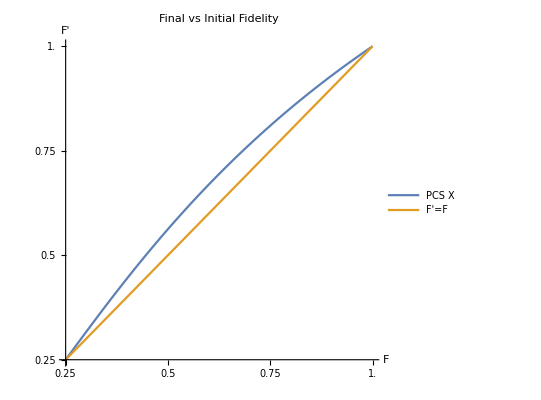

```mathematica
Plot[{fidelityInitialF, F},{F,1/4,1}, PlotLegends->Placed[{"PCS X", "F'=F"},{Right, Center}], AxesLabel->{"F", "F'"}, AspectRatio->1, PlotLabel->"Final vs Initial Fidelity", Ticks->{Range[1/4,1,0.25],Range[1/4,1,0.25]}]
```

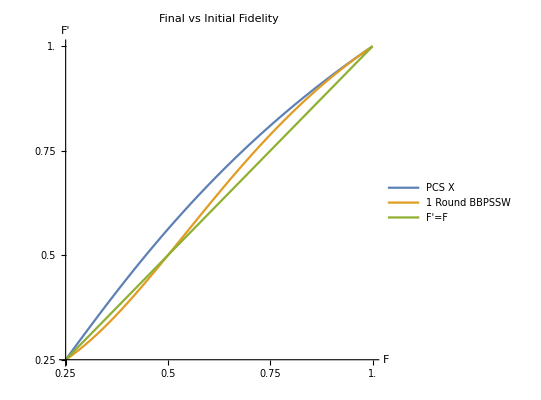

```mathematica
pcsFid[F_]:=(9 F^2)/(1+2 F)^2
bbpFid[F_]:=(F^2+((1-F)/3)^2)/(F^2+2F(1-F)/3+5(((1-F)/3))^2);
Plot[{pcsFid[F], bbpFid[F], F},{F,1/4,1},  PlotLegends->Placed[{"PCS X", "1 Round BBPSSW", "F'=F"},{.8, .4}], AxesLabel->{"F", "F'"}, AspectRatio->1, PlotLabel->"Final vs Initial Fidelity", Ticks->{Range[1/4,1,0.25],Range[1/4,1,0.25]}]
```

```mathematica
bbpFid[F]//TraditionalForm
pcsFid[F]//TraditionalForm
postrInitialF//TraditionalForm
fidelityInitialF//TraditionalForm
fidelity//TraditionalForm
```

(F^2+1/9 (1-F)^2)/(F^2+5/9 (1-F)^2+2/3 F (1-F))

(9 F^2)/(2 F+1)^2

1/9 (2 F+1)^2

(9 F^2)/(2 F+1)^2

((9 (p1-2) p1+10) p2^2+2 (20-9 p1) p1 p2+2 p1 (5 p1-12)-24 p2+16)/(4 ((p1-2) p1+2) ((p2-2) p2+2))